-0.642248+2.53478×10^-6 x

-0.128825+1.70604×10^-6 x+9.60803×10^-14 x^2

-0.0519355+1.42946×10^-6 x+1.78285×10^-13 x^2-5.77542×10^-21 x^3

-0.0400139+1.35877×10^-6 x+2.17949×10^-13 x^2-1.24843×10^-20 x^3+3.46719×10^-28 x^4

0.0889081-2.02157×10^-6 x+9.15851×10^-12 x^2-8.48395×10^-18 x^3+3.82072×10^-24 x^4-9.14639×10^-31 x^5+1.19178×10^-37 x^6-7.97176×10^-45 x^7+2.1411×10^-52 x^8

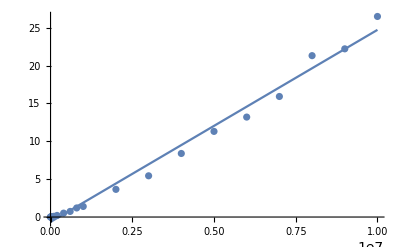

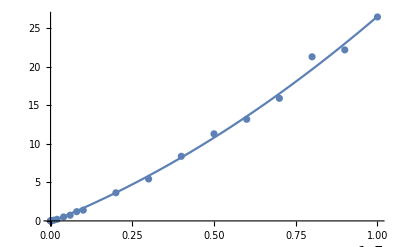

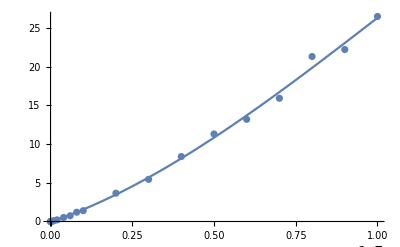

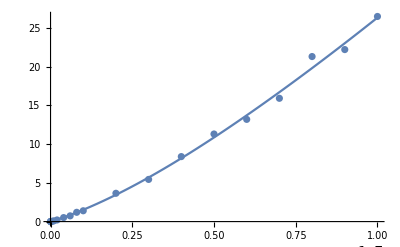

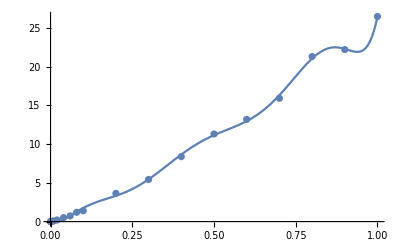

```mathematica
shell1=Fit[{{100,0.0000109672546386718},{1000,0.000222921},{5000,0.001991034},{10000,0.004676819},{50000,0.035503864},{100000,0.092874},{200000,0.210251},{400000,0.514998913},{600000,0.739268064},{800000,1.197546005},{1000000,1.395174},{2000000,3.652161121},{3000000,5.442030907},{4000000,8.388068914},{5000000,11.30365992},{6000000,13.19297218},{7000000,15.91136098},{8000000,21.30137181},{9000000,22.20038104},{10000000,26.47416902}},{1,x},x]

shell2=Fit[{{100,0.0000109672546386718},{1000,0.000222921},{5000,0.001991034},{10000,0.004676819},{50000,0.035503864},{100000,0.092874},{200000,0.210251},{400000,0.514998913},{600000,0.739268064},{800000,1.197546005},{1000000,1.395174},{2000000,3.652161121},{3000000,5.442030907},{4000000,8.388068914},{5000000,11.30365992},{6000000,13.19297218},{7000000,15.91136098},{8000000,21.30137181},{9000000,22.20038104},{10000000,26.47416902}},{1,x,x^2},x]

shell3=Fit[{{100,0.0000109672546386718},{1000,0.000222921},{5000,0.001991034},{10000,0.004676819},{50000,0.035503864},{100000,0.092874},{200000,0.210251},{400000,0.514998913},{600000,0.739268064},{800000,1.197546005},{1000000,1.395174},{2000000,3.652161121},{3000000,5.442030907},{4000000,8.388068914},{5000000,11.30365992},{6000000,13.19297218},{7000000,15.91136098},{8000000,21.30137181},{9000000,22.20038104},{10000000,26.47416902}},{1,x,x^2,x^3},x]

shell4=Fit[{{100,0.0000109672546386718},{1000,0.000222921},{5000,0.001991034},{10000,0.004676819},{50000,0.035503864},{100000,0.092874},{200000,0.210251},{400000,0.514998913},{600000,0.739268064},{800000,1.197546005},{1000000,1.395174},{2000000,3.652161121},{3000000,5.442030907},{4000000,8.388068914},{5000000,11.30365992},{6000000,13.19297218},{7000000,15.91136098},{8000000,21.30137181},{9000000,22.20038104},{10000000,26.47416902}},{1,x,x^2,x^3,x^4},x]

shell8=Fit[{{100,0.0000109672546386718},{1000,0.000222921},{5000,0.001991034},{10000,0.004676819},{50000,0.035503864},{100000,0.092874},{200000,0.210251},{400000,0.514998913},{600000,0.739268064},{800000,1.197546005},{1000000,1.395174},{2000000,3.652161121},{3000000,5.442030907},{4000000,8.388068914},{5000000,11.30365992},{6000000,13.19297218},{7000000,15.91136098},{8000000,21.30137181},{9000000,22.20038104},{10000000,26.47416902}},{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]

puntos=ListPlot[{{100,0.0000109672546386718},{1000,0.000222921},{5000,0.001991034},{10000,0.004676819},{50000,0.035503864},{100000,0.092874},{200000,0.210251},{400000,0.514998913},{600000,0.739268064},{800000,1.197546005},{1000000,1.395174},{2000000,3.652161121},{3000000,5.442030907},{4000000,8.388068914},{5000000,11.30365992},{6000000,13.19297218},{7000000,15.91136098},{8000000,21.30137181},{9000000,22.20038104},{10000000,26.47416902}}]

g1=Plot[shell1,{x,0,10000000}]
Show[puntos,g1,PlotRange->All]

g2=Plot[shell2,{x,0,10000000}]
Show[puntos,g2,PlotRange->All]

g3=Plot[shell3,{x,0,10000000}]
Show[puntos,g3,PlotRange->All]

g4=Plot[shell4,{x,0,10000000}]
Show[puntos,g4,PlotRange->All]

g8=Plot[shell8,{x,0,10000000}]
Show[puntos,g8,PlotRange->All]
```